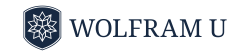

# Introduction to Probability

## Lesson 9: Continuous Random Variables

-Graphics-

## Overview

Continuous random variables imply a continuous range of values.

Continuous notations of PDF, CDF and Expectation are covered.

Useful continuous plotting functions are explained.

-Graphics-
Image Source: https://www.britannica.com/story/water-fluoridation-just-the-facts

## Probability Density Function

Continuity explains the use of density as it compares matter to probability.

For example, a polarizing poll reveals opinions are distributed with the PDF 3/2 x^2 for -1<x<1.

Use ProbabilityDistribution to model this distribution:

```mathematica
pol[x_]:=3x^2/2;
distPol =ProbabilityDistribution[pol[x],{x,-1,1}]
```

ProbabilityDistribution[(3 x^2)/2,{x,-1,1}]

## Example

Raindrops land uniformly on a triangular field measuring 20×10. What is their distribution based on length?

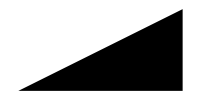

```mathematica
Graphics[Triangle[{{0,0},{2,0},{2,1}}]]
```

Since the increase is constant, the PDF is a linear function: 1/200 x for 0<=x<=20.

This is a valid PDF since the integral is 1:

```mathematica
Integrate[1/200*x,{x,0,20}]
```

1

Now, build the distribution:

```mathematica
rain[x_]:=x/200
distRain=ProbabilityDistribution[rain[x],{x,0,20}]
```

ProbabilityDistribution[x/200,{x,0,20}]

## Cumulative Distribution Function

The CDF is the cumulative version of the PDF P(x<=i) defined as an integral over the sample space:

P(x<=i)=∫PDF(x)ⅆx

In the poll example, what is the probability a random person’s disapproval is -0.5 or less?

Using a user-defined CDF:

```mathematica
polCDF[i_]:=Integrate[pol[x],{x,-1,i}]
polCDF[-0.5]
```

0.4375

## Example

In the rain example, what is the probability the raindrop falls between 5 and 10?

User-defined CDF:

```mathematica
teamCDF[s_,e_]:=Integrate[rain[x],{x,s,e}]
teamCDF[5,10]
```

3/16

CDF:

```mathematica
CDF[distRain,10]-CDF[distRain,5]
```

3/16

Probability:

```mathematica
Probability[5<=x<=10,x\[Distributed]distRain]
```

3/16

-Graphics-
Image Source: https://www.publicdomainpictures.net/en/view-image.php?image=142137&picture=rain

## Expectation

In a continuous context, the expectation is defined as:

E[f(x)]=∫f(x)P(x)ⅆx

Compute the expectation of f(x)=x on the poll example if you know the person approves:

```mathematica
Integrate[i*pol[i],{i,0,1}]/Integrate[pol[i],{i,0,1}]
```

3/4

```mathematica
Expectation[x\[Conditioned]x>0,x\[Distributed]distPol]
```

3/4

## Example

Compute the expectation of f(x)=√x on the rain example:

```mathematica
Integrate[Sqrt[i]*rain[i],{i,0,20}]
```

8/(√5)

```mathematica
Expectation[Sqrt[x],x\[Distributed]distRain]
```

8/(√5)

## Plotting

To plot continuous distributions, use the following distributions.

Plot: used most often, univariate, generates a plot of f:

```mathematica
Plot[f,{x,Subscript[x, min],Subscript[x, max]}]
```

Histogram: plots a histogram of the values x_i, plots distributions from data:

```mathematica
Histogrampaclet:ref/Histogram[{Subscript[x, 1],Subscript[x, 2],…},bspec,hspec]
```

Plot3D: bivariate, creates a three-dimensional plot of f:

```mathematica
Plot3Dpaclet:ref/Plot3D[f,{x,Subscript[x, min],Subscript[x, max]},{y,Subscript[y, min],Subscript[y, max]}]
```

Histogram3D: bivariate, plots a histogram of the values {x_i ,y_i} from bivariate data:

```mathematica
Histogram3Dpaclet:ref/Histogram3D[{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},…}]
```

## Plot

Plot the poll example distribution:

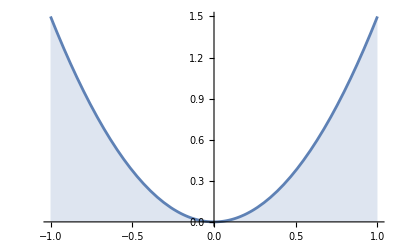

```mathematica
Plot[pol[x],{x,-1,1},Filling->Bottom]
```

```mathematica
Plot[PDF[distPol,x],{x,-1,1},Filling->Bottom]
```

-Graphics-

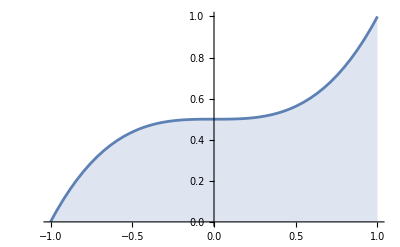

```mathematica
Plot[CDF[distPol,x],{x,-1,1},Filling->Bottom]
```

## Example

This question is taken from an old professional actuarial exam.

An insurance company insures many homes. The insured value, x, of a random home follows the PDF:

f(x)=Piecewise[{{3 x^-4,, x>1}, {0, otherwise}}]

Given a random insured home with a value of at least 1.5, calculate the probability that it is insured for less than 2.

Solve with a condition:

```mathematica
Probability[x<2\[Conditioned]x>=1.5,x\[Distributed]ProbabilityDistribution[3x^-4,{x,1,Infinity}]]
```

0.578125

## Summary

Continuous random variables have a continuous range of values.

PDF, CDF and Expectation define continuous random variables.

Useful Wolfram Language functions for plotting are Plot, Histogram, Plot3D and Histogram3D.

Many more characteristics of random variables are derived from the concept of expectation.